# Experimental Infra Bundles

We construct direction fibers from geodesic rays and compare them at different observation scales. On a cycle, one-step observations mix the two directions; longer rays separate them into a stable graph bundle. We then identify the compatibility conditions needed to retain bundle geometry under coarser observation. The ray constructions are experimental; the general graph, connection and holonomy definitions are in Infra Bundles.

## Setup

```mathematica
Needs[ "WolframInstitute`InfraGeometry`" ]
```

## Directions from finite rays

A geodesic ray of length r is a path (x_0,…,x_r) with d(x_0,x_r)==r. InfraTangentBundle takes these rays as total vertices and projects each ray to x_0. Two distinct rays are adjacent when their entries at every position match or are adjacent in the substrate graph. Thus both the fiber graph and the relations between fibers come from the substrate.

For comparison, InfraDisplacementBundle keeps only endpoint pairs at distance r. InfraCotangentBundle reverses the rays and projects to their terminal vertices. These names specify constructions; InfraFiberBundleQ tests whether the resulting finite object is a graph bundle.

The pictures show the tangent construction on C_64 at ray lengths 1, 2 and 8. Blue and orange mark the two ray orientations, arranged on concentric circles. Gray links show adjacency between rays of opposite orientation.

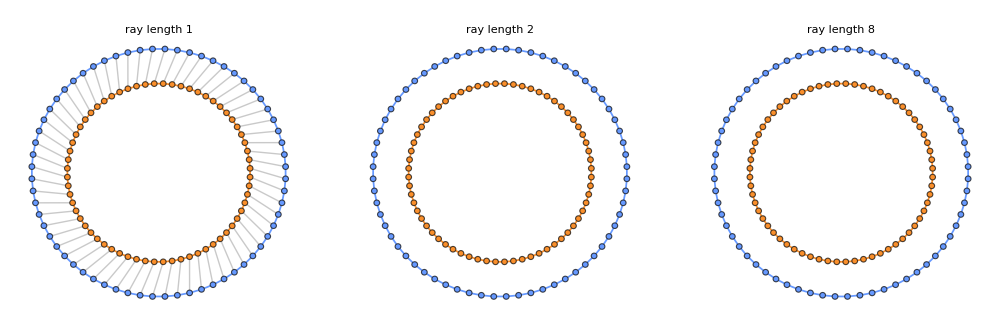

```mathematica
With[ { graph = CycleGraph[ 64 ], points = CirclePoints[ 64 ] },
  GraphicsRow[ Map[ radius |-> With[
    { total = InfraTotalSpace[ InfraTangentBundle[ graph, radius ] ] },
    { rays = VertexList[ total ] },
    { clockwise = Select[ rays, ray |-> Mod[ ray[[ 2 ]] - First[ ray ], 64 ] == 1 ] },
    InfraSubstrateHighlight[ Graph[ total, VertexLabels -> None, EdgeStyle -> GrayLevel[ .7 ],
      VertexCoordinates -> Map[ ray |->
        If[ Mod[ ray[[ 2 ]] - First[ ray ], 64 ] == 1, 1, .72 ] points[[ First[ ray ] ]], rays ],
      PlotLabel -> Row[ { "ray length ", radius } ] ],
      { Style[ Subgraph[ total, clockwise ], StandardBlue ],
        Style[ Subgraph[ total, Complement[ rays, clockwise ] ], StandardOrange ] } ,
      "ThicknessRange" -> { 1.25, 5 } ] ],
    { 1, 2, 8 } ], ImageSize -> 1000 ] ]
```

Each fiber contains a clockwise and an anticlockwise ray. At length 1, rays of opposite directions can still be adjacent above neighbouring base vertices. At length 2, their second steps separate them. The total graph becomes two disjoint cycles, one for each direction.

## See the local change

A close view of seven successive fibers explains this separation. Each vertical pair is one fiber; the two horizontal rows track its directional states. At ray length 1, gray diagonal edges allow direction change. At length 2, only the horizontal matchings remain.

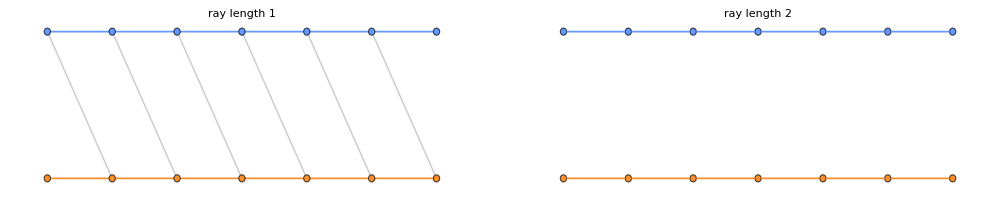

```mathematica
With[ { graph = CycleGraph[ 64 ] },
  GraphicsRow[ Map[ radius |-> With[
    { total = InfraTotalSpace[ InfraTangentBundle[ graph, radius ] ] },
    { local = Subgraph[ total, Select[ VertexList[ total ], ray |-> 29 <= First[ ray ] <= 35 ] ] },
    { rays = VertexList[ local ] },
    { clockwise = Select[ rays, ray |-> Mod[ ray[[ 2 ]] - First[ ray ], 64 ] == 1 ] },
    InfraSubstrateHighlight[ Graph[ local, VertexLabels -> None, EdgeStyle -> GrayLevel[ .7 ],
      VertexCoordinates -> Map[ ray |->
        { First[ ray ], If[ Mod[ ray[[ 2 ]] - First[ ray ], 64 ] == 1, 1, -1 ] }, rays ],
      PlotLabel -> Row[ { "ray length ", radius } ] ],
      { Style[ Subgraph[ local, clockwise ], StandardBlue ],
        Style[ Subgraph[ local, Complement[ rays, clockwise ] ], StandardOrange ] } ,
      "ThicknessRange" -> { 1.25, 5 } ] ],
    { 1, 2 } ], ImageSize -> 1000 ] ]
```

The fibers have the same size in both pictures. The graph-bundle property emerges when the extra transverse edges disappear. For this cycle, the result also has a direct proof. Write vertex labels modulo 64. For 1≤r≤31, the two rays from p are (p,p+1,…,p+r) and (p,p-1,…,p-r). Rays of the same direction above neighbouring vertices are adjacent at every position. For opposite directions above p and p+1, one pairing fails adjacency at step one and the other at step two: in each case the entries have distance 3. The same argument applies above p and p-1. The two rays in a single fiber are not adjacent, since their step-one entries have distance 2. Therefore, for 2≤r≤31 the total graph is the Cartesian product of C_64 with the discrete two-point set {+,-}.

## Compare the bundles themselves

InfraBundleMorphism supplies an explicit comparison: truncate a longer ray to its first three vertices. Each length-two ray on this cycle has a unique extension to every length up to 31. The pictures draw the two rays above one base point at lengths 2, 8 and 16. Their common two-step prefixes are drawn in stronger colors.

```mathematica
With[ { graph = CycleGraph[ 64 ] },
  GraphicsRow[ Map[ radius |-> With[
    { rays = SortBy[ InfraRays[ graph, 1, radius ], ray |-> Mod[ ray[[ 2 ]] - First[ ray ], 64 ] ],
      truncate = If[ radius == 2, Identity,
        InfraBundleMorphism[ InfraTangentBundle[ graph, radius ], InfraTangentBundle[ graph, 2 ] ] ] },
    InfraSubstrateHighlight[ Graph[ graph, GraphLayout -> "CircularEmbedding", VertexLabels -> None,
      VertexStyle -> GrayLevel[ .7 ], EdgeStyle -> GrayLevel[ .7 ],
      PlotLabel -> Row[ { "ray length ", radius } ] ],
      Join[
        MapThread[ { ray, color } |-> Style[ InfraWalk[ ray ], Lighter[ color, .4 ], AbsoluteThickness[ 2 ] ],
          { rays, { StandardBlue, StandardOrange } } ],
        MapThread[ { ray, color } |-> Style[ InfraWalk[ truncate[ ray ] ], color, AbsoluteThickness[ 3 ] ],
          { rays, { StandardBlue, StandardOrange } } ] ] ,
      "ThicknessRange" -> { 1.25, 5 } ] ], { 2, 8, 16 } ], ImageSize -> 1000 ] ]
```

-Graphics-

Truncation and extension preserve the initial vertex and the direction. By the preceding description of adjacency, they are inverse graph-bundle isomorphisms. Thus ray consistency produces two persistent directional states after the two-step threshold. The fibers are two-point sets; no vector-space structure is constructed.

## What should a coarser observation preserve?

Changing ray length, grouping vertices and adding reachability edges are distinct operations. The double-cover example in Infra Bundles gives an exact blocking rule that preserves fibers and monodromy. For a general projection π:E→B, observation maps α on total vertices and β on base vertices admit a reduced projection exactly when

α(x)==α(y)  ⟹  β(π(x))==β(π(y)).

Define the reduced projection by π̄(α(x))==β(π(x)). The condition makes this independent of the representative, and it is necessary for π̄◦α==β◦π. Reconstructing quotient adjacency gives a graph map, but lifting must still be checked.

For a fixed base, a selected transport T_pq:F_p→F_q descends through fiber equivalence relations exactly when

x∼_p y  ⟹  T_pq(x)∼_q T_pq(y).

This is again independence of the representative. Requiring the same condition for T_pq^-1 makes the descended maps inverse bijections. If the original transports preserve fiber adjacency, the descended maps preserve the reconstructed quotient fiber graphs as well. Merging base vertices requires additional compatibility with the base observation.

For the fixed base, composing the descended transports also gives a well-defined holonomy on the quotient fibers. If ρ_p is the quotient map on a starting fiber, the original and descended holonomies satisfy ρ_p H==H̄ ρ_p. This need not retain the original twist: identifying the two states in every fiber of a double cover turns its exchange into the identity on a one-point fiber.

Reachability alone can change bundle structure. Take the double cover C_32→C_16 and join total vertices at distance at most r using a graph power, while retaining the projection. The pictures use reachability radii 1, 4 and 8. Blue marks the possible steps from one total vertex, and orange marks the fiber over the opposite base vertex. At radius 8, both orange states become possible lifts of the same base step.

```mathematica
GraphicsRow[ Map[ radius |-> With[
  { total = GraphPower[ CycleGraph[ 32 ], radius ] },
  { fib = InfraFiberedGraph[ total, vertex |-> Mod[ vertex, 16, 1 ] ],
    neighbors = AdjacencyList[ total, 1 ] },
  { star = Graph[ Prepend[ neighbors, 1 ], Map[ vertex |-> UndirectedEdge[ 1, vertex ], neighbors ] ] },
  InfraFiberedGraphHighlight[ fib,
    { Style[ star, StandardBlue, AbsoluteThickness[ 2.5 ] ], Style[ InfraFiber[ fib, 9 ], StandardOrange ] },
    "BaseGraphLayout" -> "CircularEmbedding", VertexLabels -> None, EdgeStyle -> GrayLevel[ .82 ],
    PlotLabel -> Row[ { "reachability radius ", radius } ],
    "ThicknessRange" -> { 1.25, 5 } ] ],
  { 1, 4, 8 } ], ImageSize -> 1000 ]
```

-Graphics-

The threshold is exactly 8. For 1≤r≤7, the neighbours of a total vertex have offsets -r,…,-1,1,…,r along C_32. These offsets are distinct modulo 16, so each neighbouring base vertex has exactly one lift from each total vertex. At radius 8, offsets +8 and -8 first coincide modulo 16. In particular, vertices 9 and 25 both lie eight steps from vertex 1 and project to base vertex 9. Their two blue edges therefore compete to lift the same base edge. The fibers stay discrete at these radii; it is uniqueness of transverse lifting that fails. Preservation depends on the observation rule, even when the original projection is unchanged.

## A metric identity that does hold at every radius

Weak edge lifting has an exact consequence for distance balls. Let B_E(x,r) and B_B(p,r) be closed graph-distance balls of integer radius r≥0. Then InfraFibrationQ holds exactly when

π(B_E(x,r))=B_B(π(x),r)

for every total vertex x and every such radius. Every total walk projects to a base walk after consecutive repetitions are removed, without increasing length, giving the forward inclusion. For the reverse inclusion, lift a shortest base walk step by step from x. Weak edge lifting supplies every step, and the endpoint lies within total distance r. Conversely, equality at radius one supplies a transverse neighbour above every base neighbour. Thus a local lifting condition controls all finite distance scales, although it does not guarantee unique transport.

The rows compare square-grid, triangular-tiling and irregular-mesh product bundles. Each orange total ball on the left projects onto the orange base ball on the right. All three use the same four-cycle fiber and graph-distance radius, with centers chosen by GraphCenter. The projection identity holds exactly despite the different base connectivity.

The total ball contains some, but not necessarily all, of the states above each point of the base ball. Indeed, in these Cartesian products,

d_E((p,i),(q,j))==d_B(p,q)+d_C_4(i,j).

Every path must make the required number of moves in each factor, and concatenating shortest factor paths attains their sum. At base distance four, only the state with j==i lies in the radius-four total ball. Closer to the centre, the remaining distance budget admits more internal states. The projection forgets this difference and fills the whole base ball.

```mathematica
GraphicsGrid[ Map[ name |-> With[
  { base = BlockRandom[ InfraSubstrate[ name, "Medium", "KeepCoordinates" -> True ], RandomSeeding -> 2 ] },
  { fib = InfraFiberedGraph[ GraphProduct[ base, CycleGraph[ 4 ], "Cartesian" ], First ],
    point = First @ GraphCenter[ base ] },
  { totalBall = NeighborhoodGraph[ InfraTotalSpace[ fib ], { { point, 1 } }, 4 ],
    baseBall = NeighborhoodGraph[ base, { point }, 4 ] },
  { Show[ InfraFiberedGraphHighlight[ fib, Style[ totalBall, StandardOrange ], Method -> "3DFiber", VertexLabels -> None ,
    "ThicknessRange" -> { 1.25, 5 } ], BoxRatios -> { 1, 1, .02 } ],
    InfraSubstrateHighlight[ base, Style[ baseBall, StandardOrange ], VertexLabels -> None ,
      "ThicknessRange" -> { 1.25, 5 } ] } ],
  { "SquareGridGraph", "TriangularTilingGraph", "SquareMeshGraph" } ], ImageSize -> 1100 ]
```

-Graphics-

## Limits and holonomy

A continuum claim needs a sequence of substrates, a metric scaling, comparison maps and a specified convergence of total spaces, bases and projections. The ray experiment establishes a stable finite direction bundle on one substrate. Proving a topological bundle limit also requires the relevant local product structure; see Hatcher, Algebraic Topology, Section 4.2, pp. 376–377.

Fiber scaling can obstruct such a limit. If every vertical fiber is one fixed connected graph of diameter D and every total edge has length a_n, distances within a fiber are at most a_n D. When a_n→0, these fibers collapse in the total-space metric. A nontrivial limiting fiber therefore requires a different regime or additional structure.

Holonomy already has an exact coordinate-invariance statement at finite scale. Under fiber-coordinate bijections g_p, edge transport becomes g_q T_pq g_p^-1. Intermediate factors cancel around a closed walk, so its holonomy becomes g_p H g_p^-1 and its conjugacy class is unchanged. The original tutorial attributes this finite gauge interpretation to Ioana Milea's Fibered Graph Gauge Theory Basics, unpublished, 2026. Curvature additionally requires chosen faces or a loop family and an appropriate scaling of their holonomy.

Related Guides

InfraFiberBundlespaclet:WolframInstitute/InfraGeometry/guide/InfraFiberBundles ▪ Experimentalpaclet:WolframInstitute/InfraGeometry/guide/Experimental ▪ InfraTopologypaclet:WolframInstitute/InfraGeometry/guide/InfraTopology

Related Tech Notes

InfraBundlespaclet:WolframInstitute/InfraGeometry/tutorial/InfraBundles

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/ExperimentalInfraBundles

### Keywords

experimental

fibered graph

scale

observation

reduction

completion

emergence

tangent bundle

displacement bundle